{{0,1},{0.6,1.26491},{0.9,1.3784}}

P(x) =  1.+0.483656 x-0.0702286 x^2

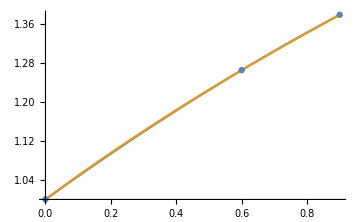

```mathematica
Clear[points,L,x,y,n,k,j,i,P]

f[t_]=√(1+t);
xs = N[{0,.6,.9},500];
points = Table[{xs⟦i⟧,f[xs⟦i⟧]},{i,1,Length[xs]}](* the interpolted points *)
a=xs⟦1⟧;b=xs⟦-1⟧;
n = Length[points] - 1;
x[k_]:=points⟦k+1⟧⟦1⟧
y[k_]:=points⟦k+1⟧⟦2⟧
Do[L[k]=1;Do[If[i≠ k ,L[k]= L[k] (x-x[i])/(x[k]-x[i])],{i,0,n}],{k,0,n}]
P[x_]=Expand[∑_(i=0)^n (y[i] L[i])];
Print["P(x) =  ", P[x]//N]
Show[Plot[{P[t],f[t]},{t,a,b}],ListPlot[points],ImageSize->Medium]
```

```mathematica
Table[{Subscript["L", i] ,L[i]},{i,0,n}]//TableForm//TraditionalForm
```

L_0 | -16.6667 (x-8.7) (x-8.6) (x-8.3)
L_1 | 41.6667 (x-8.7) (x-8.6) (x-8.1)
L_2 | -66.6667 (x-8.7) (x-8.3) (x-8.1)
L_3 | 41.6667 (x-8.6) (x-8.3) (x-8.1)

```mathematica
Maximize[{NMaximize[{D[f[t],{t,n+1}],a≤t≤b},t]⟦1⟧Abs[Product[(t-x[j]),{j,0,n}]]/(n!),a≤t≤b},t]//N
```

$Aborted